# Calculation of eikonal corrections at KE = 210 MeV

9/11/13

## Define constants

```mathematica
mp=0.938272046;(*GeV/c^2*)
mn=1.00137842*mp(*GeV/c^2*);
M=2*mp+2*mn;
m=M/4;
ℏc=0.19732697178(*Giga ElectronVolt*Femto Meter*);
r=.535^(-1/2)(*Femto Meter*);
B=1/4*r^2/ℏc^2(*(c/GeV)^2*);
A=4;
```

```mathematica
En=.210(*GeV*);
EnL=En+mp;
s=mp^2+M^2+2*M*EnL;
ϵ=EnL/(M/Sqrt[s]);
P=Sqrt[EnL^2-mp^2];
k=P*(M/Sqrt[s]);
s2=mp^2+m^2+2*m*EnL;
ϵ2=EnL*(m/Sqrt[s2]);
κ=P*(m/Sqrt[s2]);
ηO=(1-ϵ/M)*(mp+M)/Sqrt[s];
ηD=(1-ϵ/ϵ2+(A-1)*ϵ/M)*(mp+M)/Sqrt[s];
```

```mathematica
(1/4/ℏc)^2/6
```

0.26752

```mathematica
Sqrt[6 B]*ℏc
```

1.67444

```mathematica
1.25*4^(1/3)
```

1.98425

## Import data and convert it from degrees and mbarn^1/2 to momentum transfer and fm

```mathematica
(*pp210a=Import["/Users/Micah/Documents/JerryDuty/eikexp/pp210a.csv"];
pp210b=Import["/Users/Micah/Documents/JerryDuty/eikexp/pp210b.csv"];*)
```

```mathematica
pp210a=Import["/phys/users/mbuuck/JerryDuty/eikexp/pp210a.csv"];
pp210b=Import["/phys/users/mbuuck/JerryDuty/eikexp/pp210b.csv"];
```

```mathematica
pp210a=Transpose[{pp210a[[All,1]],pp210a[[All,2]]+I*pp210a[[All,3]]}];
pp210b=Transpose[{pp210b[[All,1]],pp210b[[All,2]]+I*pp210b[[All,3]]}];
```

```mathematica
θpp210=Transpose[{pp210a[[All,1]],(pp210a[[All,2]]+pp210b[[All,2]])/2}];
```

```mathematica
θtoq[x_]:={2 κ Sin[x[[1]] Pi/360],x[[2]]/Sqrt[10]}
```

```mathematica
pp210=θtoq/@θpp210;
```

```mathematica
(*pn210a=Import["/Users/Micah/Documents/JerryDuty/eikexp/pn210a.csv"];
pn210b=Import["/Users/Micah/Documents/JerryDuty/eikexp/pn210b.csv"];*)
```

```mathematica
pn210a=Import["/phys/users/mbuuck/JerryDuty/eikexp/pn210a.csv"];
pn210b=Import["/phys/users/mbuuck/JerryDuty/eikexp/pn210b.csv"];
```

```mathematica
pn210a=Transpose[{pn210a[[All,1]],pn210a[[All,2]]+I*pn210a[[All,3]]}];
pn210b=Transpose[{pn210b[[All,1]],pn210b[[All,2]]+I*pn210b[[All,3]]}];
```

```mathematica
θpn210=Transpose[{pn210a[[All,1]],(pn210a[[All,2]]+pn210b[[All,2]])/2}];
```

```mathematica
pn210=θtoq/@θpn210;
```

```mathematica
NN210=(pp210+pn210)/2;
```

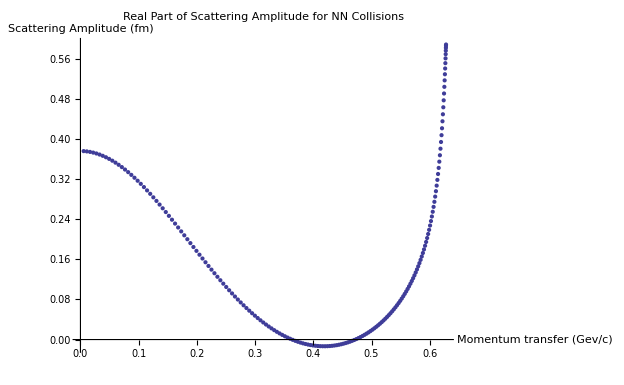

```mathematica
ListPlot[Transpose[{NN210[[All,1]],Re[NN210[[All,2]]]}],PlotLabel->"Real Part of Scattering Amplitude for NN Collisions",AxesLabel->{"Momentum transfer (Gev/c)","Scattering Amplitude (fm)"}]
```

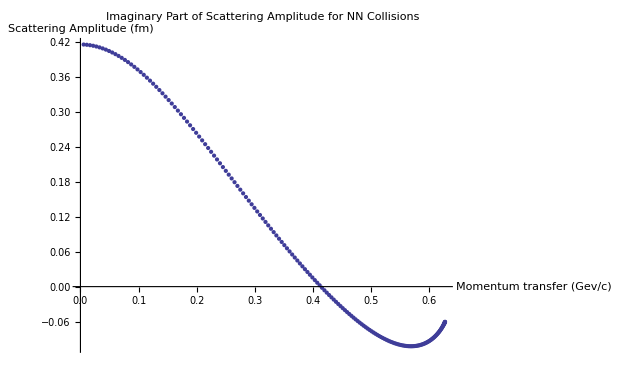

```mathematica
ListPlot[Transpose[{NN210[[All,1]],Im[NN210[[All,2]]]}],PlotLabel->"Imaginary Part of Scattering Amplitude for NN Collisions",AxesLabel->{"Momentum transfer (Gev/c)","Scattering Amplitude (fm)"}]
```

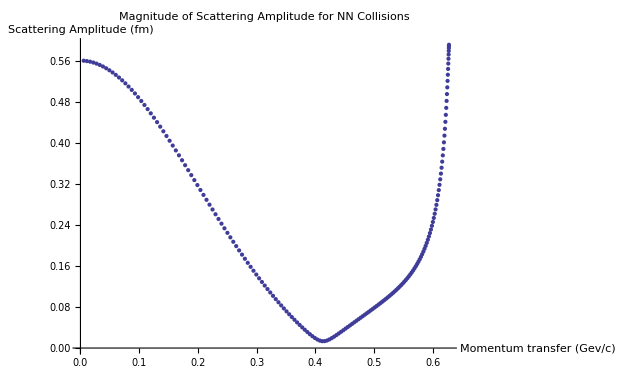

```mathematica
ListPlot[Transpose[{NN210[[All,1]],Abs[NN210[[All,2]]]}],PlotLabel->"Magnitude of Scattering Amplitude for NN Collisions",AxesLabel->{"Momentum transfer (Gev/c)","Scattering Amplitude (fm)"}]
```

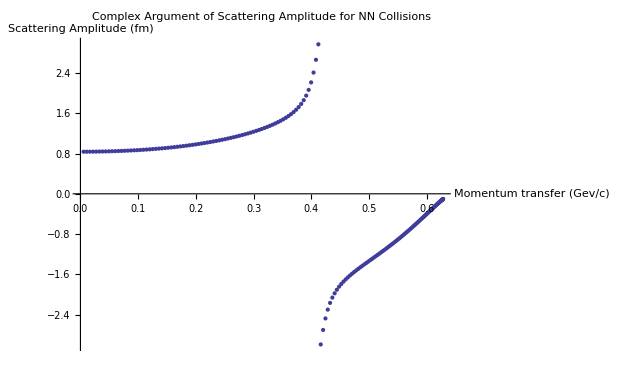

```mathematica
ListPlot[Transpose[{NN210[[All,1]],Arg[NN210[[All,2]]]}],PlotLabel->"Complex Argument of Scattering Amplitude for NN Collisions",AxesLabel->{"Momentum transfer (Gev/c)","Scattering Amplitude (fm)"}]
```

## Fit data to complex gaussian (see model on next line)

```mathematica
Clear[β,ρ,σ]
model=κ σ (I+ρ)/(4 Pi) Exp[-β q^2];
```

The fit is only performed over the first 50 degrees.

```mathematica
Clear[σ]
```

{a→0.562662,βre→14.4438}

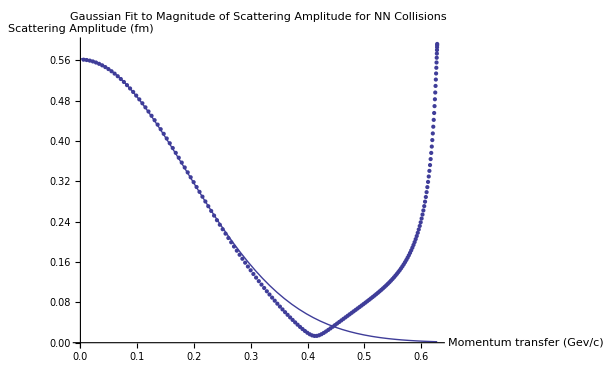

```mathematica
Npts=50;
FindFit[Transpose[{NN210[[1;;Npts,1]],Abs[NN210[[1;;Npts,2]]]}],a Exp[-βre q^2],{a,βre},q]
Show[Plot[a Exp[-βre q^2]/.%,{q,0,2 κ}],ListPlot[Transpose[{NN210[[All,1]],Abs[NN210[[All,2]]]}]],PlotLabel->"Gaussian Fit to Magnitude of Scattering Amplitude for NN Collisions",AxesLabel->{"Momentum transfer (Gev/c)","Scattering Amplitude (fm)"},PlotRange->All]
```

```mathematica
(4.18-I 2.70) Exp[-(16-I 5.66) q^2]/(2 I κ)
```

{ρ→0.916394,βim→-3.97743}

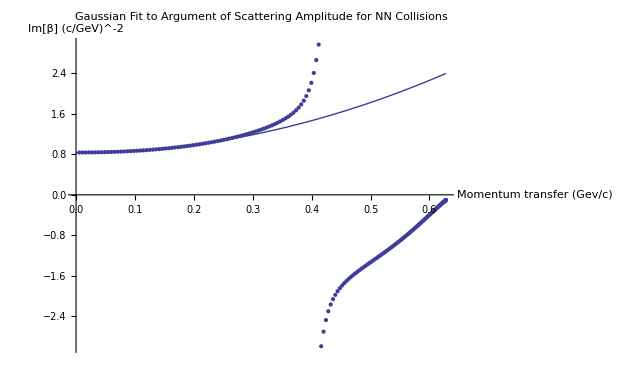

```mathematica
FindFit[Transpose[{NN210[[1;;Npts,1]],Arg[NN210[[1;;Npts,2]]]}],ArcTan[ρ,1]-βim q^2,{ρ,βim},q]
Show[ListPlot[Transpose[{NN210[[All,1]],Arg[NN210[[All,2]]]}]],Plot[ArcTan[ρ,1]-βim q^2/.%,{q,0,2 κ}],PlotLabel->"Gaussian Fit to Argument of Scattering Amplitude for NN Collisions",AxesLabel->{"Momentum transfer (Gev/c)","Im[β] (c/GeV)^-2"}]
```

```mathematica
NSolve[κ/ℏc σ Sqrt[1+ρ^2]/(4 Pi)==0.5626620954511277&&ρ==0.9163935163116479,{σ,ρ}]
```

{{σ→3.27607,ρ→0.916394}}

Fitted parameters:

```mathematica
σ=3.2760668043032632;
ρ=0.9163935163116479;
β=14.4437913447594-3.977429080580476 I;
```

## Glauber

```mathematica
σ1=-σ/ℏc^2 (1-I ρ)/(8 Pi β)
Fcm[q_]:=Exp[B*q^2/A]
```

-0.269799+0.138098 ⅈ

```mathematica
F0[q_]:=-2*I*k*Fcm[q]*(B+β)*Sum[Binomial[A,j]/j*(-σ (1-I ρ)/ℏc^2/(8 Pi (B+β)))^j*Exp[-(B+β)*q^2/j],{j,1,A}]*ℏc
```

Glauber approximation  for p-α scattering is below:

```mathematica
40*Pi/(k/ℏc) Im[F0[0]]
```

125.188

## Add in First Order Correction

```mathematica
Γ[b_]:=σ1 Exp[-b^2/(4 β)]
```

```mathematica
Γ[0]
```

-0.269799+0.138098 ⅈ

```mathematica
ρ0[r_]:=(4 Pi B)^(-3/2) Exp[-r^2/(4 B)]
```

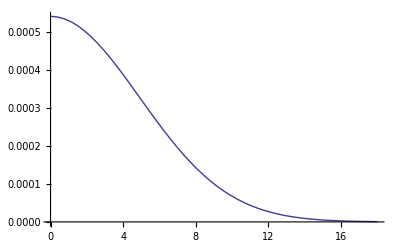

```mathematica
Plot[ρ0[r],{r,0,18}]
```

```mathematica
U[q_]:=2*Pi*I*NIntegrate[b*BesselJ[0,b*q]*Log[1-Γ[b]],{b,0,Infinity}]
```

```mathematica
U[0]
```

35.0029+40.535 ⅈ

Wallace parameterizes it as a gaussian in q, so we should check the validity of that assertion:

```mathematica
Quiet[Table[{q,Abs[U[Sqrt[q]]/(-I 4 Pi β σ1)]},{q,0,1,.01}]]
```

{{0.,0.938597},{0.01,0.80905},{0.02,0.697222},{0.03,0.600708},{0.04,0.517426},{0.05,0.445576},{0.06,0.383602},{0.07,0.330159},{0.08,0.284083},{0.09,0.24437},{0.1,0.210151},{0.11,0.180673},{0.12,0.155289},{0.13,0.133437},{0.14,0.114633},{0.15,0.0984573},{0.16,0.0845491},{0.17,0.0725958},{0.18,0.0623276},{0.19,0.0535117},{0.2,0.045947},{0.21,0.0394598},{0.22,0.0339004},{0.23,0.0291394},{0.24,0.0250652},{0.25,0.0215816},{0.26,0.0186053},{0.27,0.0160647},{0.28,0.0138978},{0.29,0.0120512},{0.3,0.0104786},{0.31,0.00914004},{0.32,0.00800113},{0.33,0.00703201},{0.34,0.00620695},{0.35,0.00550374},{0.36,0.00490329},{0.37,0.00438921},{0.38,0.00394753},{0.39,0.00356638},{0.4,0.00323577},{0.41,0.0029473},{0.42,0.00269402},{0.43,0.00247015},{0.44,0.00227098},{0.45,0.00209265},{0.46,0.00193199},{0.47,0.00178647},{0.48,0.00165399},{0.49,0.00153287},{0.5,0.00142172},{0.51,0.0013194},{0.52,0.00122498},{0.53,0.00113767},{0.54,0.0010568},{0.55,0.000981806},{0.56,0.000912195},{0.57,0.000847541},{0.58,0.000787462},{0.59,0.000731622},{0.6,0.000679715},{0.61,0.000631463},{0.62,0.000586612},{0.63,0.000544927},{0.64,0.000506193},{0.65,0.000470209},{0.66,0.000436787},{0.67,0.000405752},{0.68,0.000376943},{0.69,0.000350205},{0.7,0.000325396},{0.71,0.000302384},{0.72,0.000281042},{0.73,0.000261254},{0.74,0.00024291},{0.75,0.000225908},{0.76,0.000210153},{0.77,0.000195554},{0.78,0.000182029},{0.79,0.000169499},{0.8,0.000157892},{0.81,0.00014714},{0.82,0.000137181},{0.83,0.000127955},{0.84,0.000119408},{0.85,0.000111489},{0.86,0.000104151},{0.87,0.0000973506},{0.88,0.0000910466},{0.89,0.0000852015},{0.9,0.0000797803},{0.91,0.0000747507},{0.92,0.0000700826},{0.93,0.0000657484},{0.94,0.0000617223},{0.95,0.0000579807},{0.96,0.0000545016},{0.97,0.0000512648},{0.98,0.0000482516},{0.99,0.0000454449},{1.,0.0000428288}}

```mathematica
interp1=Interpolation[{{0.,0.9385969032068576},{0.01,0.80904982036998},{0.02,0.6972224665358752},{0.03,0.6007081779780753},{0.04,0.5174257602441585},{0.05,0.4455755876676835},{0.06,0.38360161555444094},{0.07,0.33015850931970586},{0.08,0.28408320189273734},{0.09,0.2443702833473142},{0.1,0.21015070689800686},{0.11,0.18067336479678026},{0.12,0.15528914772374616},{0.13,0.13343715324480843},{0.14,0.11463275389386228},{0.15,0.09845727436883633},{0.16,0.0845490610229667},{0.17,0.07259575599040465},{0.18,0.062327613519038365},{0.19,0.05351171792261722},{0.2,0.045946981468214104},{0.21,0.03945981688326324},{0.22,0.03390039334707626},{0.23,0.029139397129646184},{0.24,0.025065228723125606},{0.25,0.021581577613599762},{0.26,0.01860532396769858},{0.27,0.016064723634798127},{0.28,0.013897839131120453},{0.29,0.012051184774574569},{0.3,0.010478558924511307},{0.31,0.009140040337381949},{0.32,0.008001128917481238},{0.33,0.007032013545768064},{0.34,0.006206951180384425},{0.35000000000000003,0.0055037421377275705},{0.36,0.004903286666601617},{0.37,0.004389208077804809},{0.38,0.003947528303615294},{0.39,0.003566383218078125},{0.4,0.003235767420916504},{0.41000000000000003,0.0029473011826013974},{0.42,0.0026940153247033663},{0.43,0.0024701524041998366},{0.44,0.0022709843071154518},{0.45,0.0020926471453063394},{0.46,0.0019319943484238076},{0.47000000000000003,0.0017864683416603437},{0.48,0.0016539904983889232},{0.49,0.0015328683842624061},{0.5,0.0014217187966769967},{0.51,0.001319404795774196},{0.52,0.0012249848072989568},{0.53,0.0011376719120468836},{0.54,0.0010568015720190174},{0.55,0.000981806235412397},{0.56,0.0009121954769475277},{0.5700000000000001,0.0008475405433054375},{0.58,0.0007874623714074275},{0.59,0.0007316223225829214},{0.6,0.0006797150259554576},{0.61,0.0006314628499490188},{0.62,0.0005866116238404889},{0.63,0.0005449273145259381},{0.64,0.0005061934301237543},{0.65,0.0004702089746029066},{0.66,0.0004367868188704648},{0.67,0.0004057523858310616},{0.68,0.00037694257182959795},{0.6900000000000001,0.0003502048460040953},{0.7000000000000001,0.0003253964837503729},{0.71,0.00030238390166780827},{0.72,0.0002810420698163009},{0.73,0.0002612539835071025},{0.74,0.00024291018163248882},{0.75,0.00022590830209728922},{0.76,0.00021015266755729364},{0.77,0.00019555389658889712},{0.78,0.00018202853682841756},{0.79,0.00016949871761363035},{0.8,0.00015789182036545854},{0.81,0.00014714016545238945},{0.8200000000000001,0.0001371807146055566},{0.8300000000000001,0.00012795478815401273},{0.84,0.00011940779651995292},{0.85,0.00011148898545021908},{0.86,0.00010415119453865222},{0.87,0.00009735062858425798},{0.88,0.00009104664132877913},{0.89,0.00008520153114166202},{0.9,0.0000797803481499004},{0.91,0.00007475071237153883},{0.92,0.00007008264234563396},{0.93,0.0000657483937638765},{0.9400000000000001,0.0000617223076398291},{0.9500000000000001,0.0000579806674986},{0.96,0.000054501565148787386},{0.97,0.00005126477454996199},{0.98,0.000048251633344614576},{0.99,0.00004544493163198942},{1.,0.00004282880758918227}}];
```

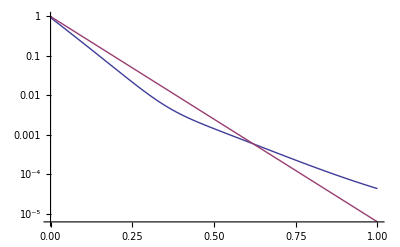

```mathematica
Quiet[LogPlot[{interp1[t],Exp[-B t]},{t,0,1}]]
```

The magnitude seems to be well approximated by a gaussian.

```mathematica
Quiet[Table[{q,Arg[U[Sqrt[q]]/(-I 4 Pi β σ1)]},{q,0,1,.01}]]
```

{{0.,0.0295053},{0.01,0.0728101},{0.02,0.116474},{0.03,0.160532},{0.04,0.205021},{0.05,0.249982},{0.06,0.295462},{0.07,0.341509},{0.08,0.388178},{0.09,0.435529},{0.1,0.483627},{0.11,0.532543},{0.12,0.582355},{0.13,0.633149},{0.14,0.685017},{0.15,0.738059},{0.16,0.792386},{0.17,0.848113},{0.18,0.905368},{0.19,0.964282},{0.2,1.025},{0.21,1.08766},{0.22,1.15241},{0.23,1.21941},{0.24,1.2888},{0.25,1.36069},{0.26,1.43522},{0.27,1.51245},{0.28,1.59242},{0.29,1.67512},{0.3,1.76047},{0.31,1.84831},{0.32,1.93839},{0.33,2.03038},{0.34,2.12385},{0.35,2.21832},{0.36,2.31324},{0.37,2.40805},{0.38,2.50218},{0.39,2.5951},{0.4,2.68633},{0.41,2.77549},{0.42,2.86226},{0.43,2.94642},{0.44,3.02785},{0.45,3.10648},{0.46,-3.10086},{0.47,-3.02775},{0.48,-2.95726},{0.49,-2.88929},{0.5,-2.82367},{0.51,-2.76027},{0.52,-2.69891},{0.53,-2.63944},{0.54,-2.58171},{0.55,-2.52555},{0.56,-2.47083},{0.57,-2.41741},{0.58,-2.36516},{0.59,-2.31396},{0.6,-2.2637},{0.61,-2.21427},{0.62,-2.16558},{0.63,-2.11754},{0.64,-2.07006},{0.65,-2.02307},{0.66,-1.9765},{0.67,-1.93027},{0.68,-1.88434},{0.69,-1.83864},{0.7,-1.79313},{0.71,-1.74776},{0.72,-1.70249},{0.73,-1.65728},{0.74,-1.6121},{0.75,-1.56691},{0.76,-1.5217},{0.77,-1.47644},{0.78,-1.4311},{0.79,-1.38568},{0.8,-1.34017},{0.81,-1.29454},{0.82,-1.24881},{0.83,-1.20296},{0.84,-1.157},{0.85,-1.11093},{0.86,-1.06475},{0.87,-1.01848},{0.88,-0.972125},{0.89,-0.925697},{0.9,-0.879212},{0.91,-0.832689},{0.92,-0.786146},{0.93,-0.739602},{0.94,-0.693079},{0.95,-0.646599},{0.96,-0.600184},{0.97,-0.553856},{0.98,-0.50764},{0.99,-0.461556},{1.,-0.415627}}

```mathematica
interp2=Interpolation[{{0.,0.029505261608375275},{0.01,0.07281014694288646},{0.02,0.1164742070391524},{0.03,0.16053186314920545},{0.04,0.20502083323737644},{0.05,0.24998245338622557},{0.06,0.2954620279430167},{0.07,0.34150920918466243},{0.08,0.3881784064311773},{0.09,0.43552922325510074},{0.1,0.4836269195584356},{0.11,0.5325428926079314},{0.12,0.5823551673595684},{0.13,0.6331488812140369},{0.14,0.6850167412904351},{0.15,0.7380594228584028},{0.16,0.7923858651213993},{0.17,0.8481134044449281},{0.18,0.9053676647657719},{0.19,0.9642820999061941},{0.2,1.0249970529602064},{0.21,1.087658164906085},{0.22,1.1524139309085137},{0.23,1.219412173843458},{0.24,1.2887951896818215},{0.25,1.3606933327329114},{0.26,1.4352168700441135},{0.27,1.5124460673583129},{0.28,1.5924196975187244},{0.29,1.6751224998571586},{0.3,1.760472554734834},{0.31,1.848310016543234},{0.32,1.9383890596297464},{0.33,2.0303750711956794},{0.34,2.1238488959458675},{0.35000000000000003,2.218319183801109},{0.36,2.313242651157149},{0.37,2.4080505801754652},{0.38,2.5021785572159465},{0.39,2.5950957182162235},{0.4,2.6863298819522163},{0.41000000000000003,2.775485871327662},{0.42,2.8622557313003303},{0.43,2.9464210091908325},{0.44,3.0278483935218743},{0.45,3.1064806224016053},{0.46,-3.100860625505517},{0.47000000000000003,-3.027746250580996},{0.48,-2.9572639488650587},{0.49,-2.889288137051846},{0.5,-2.823674762148799},{0.51,-2.7602690307094426},{0.52,-2.69891144488232},{0.53,-2.6394423376331066},{0.54,-2.581705146348759},{0.55,-2.525548668490619},{0.56,-2.4708285233236986},{0.5700000000000001,-2.4174080128863435},{0.58,-2.365158541500214},{0.59,-2.3139597207525715},{0.6,-2.2636992584946722},{0.61,-2.214272706541138},{0.62,-2.165583122539053},{0.63,-2.1175406863875703},{0.64,-2.0700622998575042},{0.65,-2.0230711892536895},{0.66,-1.976496524457649},{0.67,-1.930273062630312},{0.68,-1.8843408215359976},{0.6900000000000001,-1.8386447846304133},{0.7000000000000001,-1.7931346384423366},{0.71,-1.7477645412854688},{0.72,-1.7024929215234095},{0.73,-1.657282302897021},{0.74,-1.6120991539718774},{0.75,-1.5669137584422976},{0.76,-1.5217001027869341},{0.77,-1.4764357777013086},{0.78,-1.4311018894844938},{0.79,-1.385682977677722},{0.8,-1.3401669352617371},{0.81,-1.2945449277058625},{0.8200000000000001,-1.2488113073580411},{0.8300000000000001,-1.2029635200769317},{0.84,-1.1570020009102715},{0.85,-1.11093005649656},{0.86,-1.0647537318652218},{0.87,-1.0184816602079072},{0.88,-0.9721248947213316},{0.89,-0.9256967219733012},{0.9,-0.8792124576468394},{0.91,-0.8326892253310385},{0.92,-0.7861457203979536},{0.93,-0.739601961543195},{0.9400000000000001,-0.693079032646209},{0.9500000000000001,-0.646598818863139},{0.96,-0.6001837403747358},{0.97,-0.5538564881023169},{0.98,-0.5076397653848028},{0.99,-0.4615560395646657},{1.,-0.415627307189527}}];
```

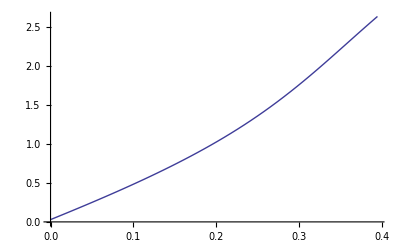

```mathematica
Quiet[Plot[interp2[t],{t,0,(2 κ)^2}]]
```

```mathematica
Quiet[U[.1]]
```

28.6309+36.2137 ⅈ

```mathematica
γ=100*Quiet[(Log[U[0]]-Log[U[0.1]])]
```

14.8526-4.33049 ⅈ

```mathematica
Z=U[0]/(-I*4*Pi*σ1*β)(*Unitless*)
```

0.938188+0.0276895 ⅈ

Here are a bunch of parameters that Wallace has defined in his paper.

```mathematica
γ1:=γ*β/(γ+β)(*(c/GeV)^2*)
αnL[n_,L_]:=If[n==1,(2*(γ+B)^-1+L*(β+B)^-1)^-1,If[n==2,((γ+B)^-1+(γ1+B)^-1+L*(β+B)^-1)^-1,If[n==3,(2*(γ1+B)^-1+L*(β+B)^-1)^-1]]]
an[n_]:=If[n==1,(γ+B)^-2,If[n==2,-2*σ1*(γ1/γ)*(γ+B)^-1*(γ1+B)^-1,If[n==3,σ1^2*(γ1/γ)^2*(γ1+B)^-2]]]
bn[n_]:=If[n==1,(γ+B)^-3,If[n==2,-σ1*(γ1/γ)*(γ1+B)^-1*(γ+B)^-1*((1-B*γ1/(β*(B+γ1)))/(γ+B)+(1-γ1/β)/(γ1+B)),If[n==3,σ1^2*(γ1/γ)^2*(γ1+B)^-3*(1-B*γ1/(β*(B+γ1)))*(1-γ1/β)]]]
γ2:=γ*β/(β+2*γ)(*(c/GeV)^2*)
βnL[n_,L_]:=If[n==1,((γ/2+B)^-1+L*(β+B)^-1)^-1,If[n==2,((γ2/2+B)^-1+L*(β+B)^-1)^-1]]
cn[n_]:=If[n==1,(γ-2*B)*(γ+2*B)^-2,If[n==2,-σ1(γ2/γ1)*(γ2+2*B)^-1*(1-2*γ2/γ+2*(γ2)^2/(γ*(γ2+2*B)))]]
dn[n_]:=If[n==1,γ*(γ+2*B)^-3,If[n==2,
-σ1*(γ)^-2*(γ2/(γ2+2*B))^3]]
```

```mathematica
FO1[q_(*c/GeV*)]:=A*(A-1)*Fcm[q]*ηO*(β*σ1*Z)^2/(2*(2*Pi*(B+β))^(1/2))*Sum[Binomial[A-2,L]*(-σ1*β/(B+β))^L*Sum[αnL[n,L]*(an[n]-4*αnL[n,L]*bn[n]*(1-αnL[n,L]q^2))*Exp[-αnL[n,L]*q^2],{n,1,3}],{L,0,A-2}]*ℏc
```

```mathematica
FD1[q_(*c/GeV*)]:=A*Fcm[q]*ηD*(β*σ1*Z)^2/(2*γ*Sqrt[2*Pi*γ])*Sum[Binomial[A-1,L]*(-σ1*β/(B+β))^L*Sum[βnL[n,L]*(cn[n]-4*βnL[n,L]*dn[n]*(1-βnL[n,L]*q^2))*Exp[-βnL[n,L]*q^2],{n,1,2}],{L,0,A-1}]*ℏc
```

```mathematica
Im[FO1[0]+FD1[0]]/Im[F0[0]+FO1[0]+FD1[0]]
```

0.00256045

The first order correction is about 0.3% at 210 MeV.

```mathematica
40*Pi/(k/ℏc) Im[F0[0]]
40*Pi/(k/ℏc) Im[FO1[0]+FD1[0]]
40*Pi/(k/ℏc) Im[FO1[0]+FD1[0]+F0[0]]
```

125.188

0.321361

125.51

```mathematica
FO1[0]
```

-0.00652947+0.0182865 ⅈ

```mathematica
FD1[0]
```

0.0067961-0.0116559 ⅈ